## Formulas

```mathematica
P(Subscript[E, ν])=Piecewise[{{Subscript[E, ν]^2(Subscript[Q, β]-Subscript[E, ν])√((Subscript[Q, β]-Subscript[E, ν])^2-Subscript[m, e]^2), ,0<Subscript[E, ν]<Subscript[Q, β]-Subscript[m, e]}, {0, ,Subscript[E, ν]>Subscript[Q, β]-Subscript[m, e]}}]
```

```mathematica
Subscript[C, 0]=(1-e^(-Subscript[λ, o]t))y   ,        i=0
Subscript[C, i]=(1-e^(-Subscript[λ, i]t))Subscript[C, i-1]   ,  i > 0,  i=0.. Subscript[k, n]-число элементов в  n-той цепочке распада
```

```mathematica
S(Subscript[E, ν],t) = ∑_n ∑_i^Subscript[k, n] Subscript[P, i](Subscript[E, ν]) Subscript[C, i](t)
```

## Load files with data

```mathematica
elements={"u235","pu239"};
plotNames={"1s","1minute","1hour","24hours","1year"(*,"1week"*)};
forPlot={};
```

```mathematica
For[i=1,i≤Length@elements,i++,
filenames =FileNameJoin[{NotebookDirectory[],elements[[i]]<>"time"<>#<>".dat"}]&/@plotNames;
data=Import[#,"Data"]&/@filenames;
AppendTo[forPlot,elements[[i]]->data]
]
(*maximumData=Import[FileNameJoin[{NotebookDirectory[],"maximum_time.dat"}],"Data"];*)
```

## Neutrino spectrum plots

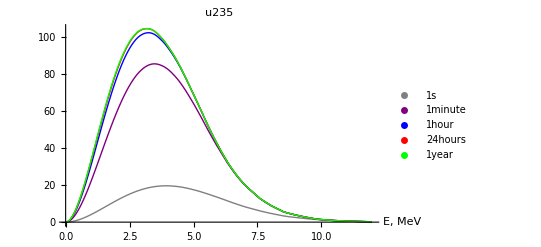

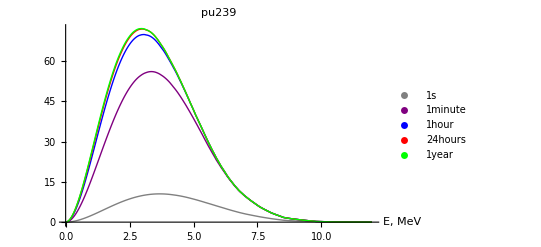

```mathematica
ListPlot[forPlot[[1,2]],PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[1,1]]]
ListPlot[forPlot[[2,2]],PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames,
PlotRange->{{0,12},Automatic},PlotLabel->forPlot[[2,1]]]
```

```mathematica
pos1year=Position[plotNames,"1year"][[1,1]];
u235year=forPlot[[1,2,pos1year]];
pu239year=forPlot[[2,2,pos1year]];
ratio=u235year[[All,2]]/pu239year[[All,2]];
ratioPlot={};
For[i=2,i≤Length@ratio,i++,AppendTo[ratioPlot,{u235year[[i,1]],ratio[[i]]}]]
```

```mathematica
ratioPlot;
```

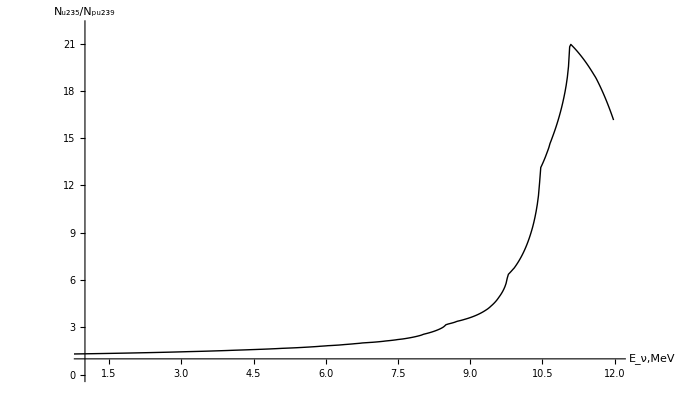

```mathematica
ListPlot[ratioPlot,PlotRange->{{1,12},{0,22}},AxesOrigin->{1,1},Joined->True,AxesLabel->{"E_ν,MeV","N_u235/N_pu239"},PlotStyle->Black]
```

## Normalized plots

```mathematica
dataNormalized={};
data=forPlot[[1,2]];
For[i=1,i≤Length@data,i++,
AppendTo[dataNormalized,
{#[[1]],#[[2]]/Max[data[[i]][[All,2]]]}&/@data[[i]]
]
]
```

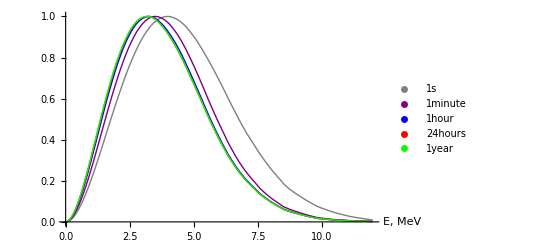

```mathematica
ListPlot[dataNormalized,PlotStyle->{Gray,Purple,Blue,Red,Green},AxesLabel->{"E, MeV"},Joined->True,PlotLegends->plotNames]
```

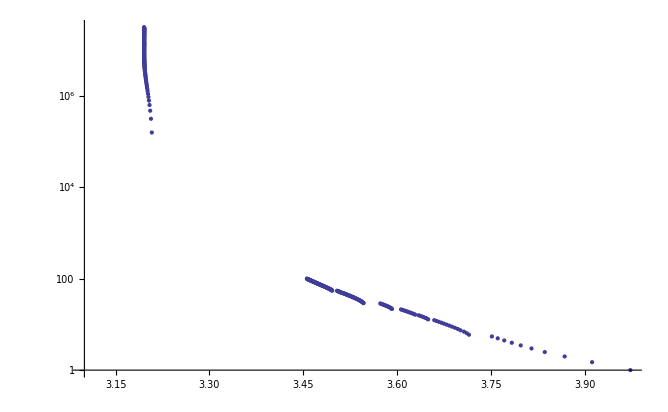

```mathematica
ListLogPlot[maximumData,PlotRange->All,AxesOrigin->{3.1,0}]
```